```mathematica
constantSignalValue = 0.3;
(* from here we assume sample count of 1000 *)
sampleCount = 1000;
originalConstantSignal = constantSignalValue&/@Range[sampleCount];
(* 1 bit quantization of constant signal of 1000 samples *)
quantizedSignal = Round[constantSignalValue]&/@Range[sampleCount];
SetDirectory@NotebookDirectory[];
```

```mathematica
signalError = originalConstantSignal-quantizedSignal;
```

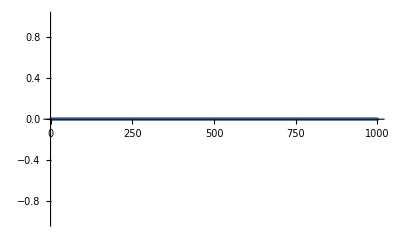

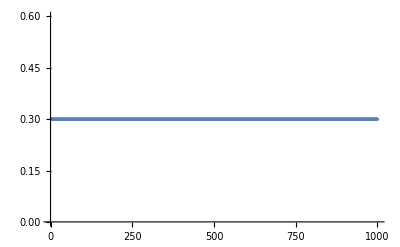

```mathematica
ListPlot[quantizedSignal]
ListPlot[signalError]
(* Plot of quantized signal *)
```

```mathematica
(* Plot of quantization error *)
```

```mathematica
(*As expected, average of signal error is 0.3 *)
Mean[signalError]
```

0.3

```mathematica
(* Same qantization, but with dithering in range -0.5, 0.5 *)
```

```mathematica
quantizedDitheredSignal = Round[constantSignalValue+RandomReal[]-0.5]&/@Range[sampleCount];
```

```mathematica
(* Plot of quantized dithered signal *)
```

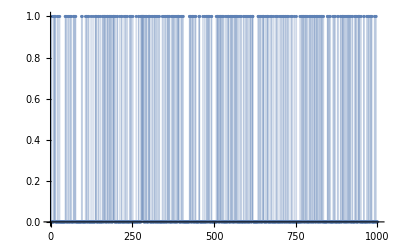

```mathematica
ListPlot[quantizedDitheredSignal,Filling->Axis]
```

```mathematica
Image[Join[{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},{quantizedDitheredSignal},1]]
```

-Graphics-

```mathematica
(*Dithered signal error *)
```

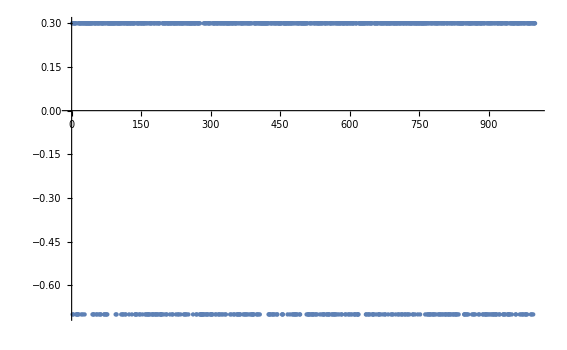

```mathematica
ditheredSignalError = originalConstantSignal-quantizedDitheredSignal;
ListPlot[ditheredSignalError]
```

```mathematica
Mean[ditheredSignalError]
```

-0.022

```mathematica
0.02800000000000019
```

0.028

```mathematica
MyPeriodogram[x_,col_:Black,range_:Full]:=ListPlot[Abs@Fourier[x][[;;sampleCount/2]],PlotRange->range,Filling->Axis,FillingStyle->{Thickness[0.05],col}]
```

```mathematica
(*Frequency plot of error signal*)
```

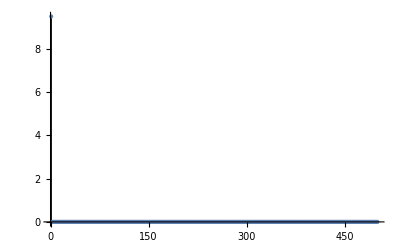

```mathematica
MyPeriodogram[signalError]
```

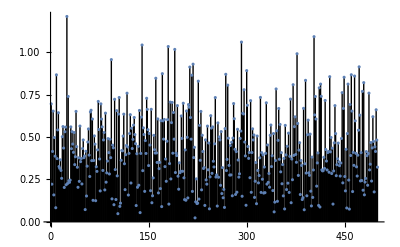

```mathematica
MyPeriodogram[ditheredSignalError]
```

```mathematica
ListAnimate[{MyPeriodogram[signalError,Red,{0,10}],MyPeriodogram[ditheredSignalError,Black,{0,10}]}]
```

```mathematica
Export["spectrum_quantization_noise_comparison.gif",{MyPeriodogram[signalError,Red,{0,10}],MyPeriodogram[ditheredSignalError,Black,{0,10}]},"DisplayDurations"->2];
```

```mathematica
MyFilter[x_]:=RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{5,0.1}],1],x,Padding->"Fixed"]
```

```mathematica
(* Plot low pass filter applied on quantized signal and its error *)
```

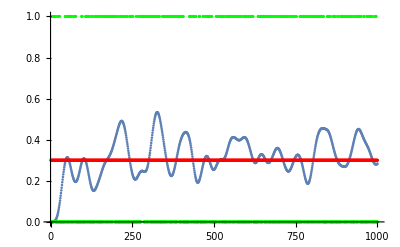

```mathematica
Show[ListPlot[MyFilter[quantizedDitheredSignal],PlotRange->{0,1}],ListPlot[originalConstantSignal,PlotStyle->Red],ListPlot[quantizedDitheredSignal,PlotStyle->Green]]
```

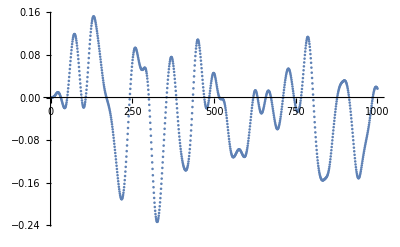

```mathematica
ListPlot[MyFilter[ditheredSignalError]]
```

```mathematica
(*Let's try a different dithering noise function*)
```

```mathematica
quantizedDitheredSignalGolden = Round[constantSignalValue+FractionalPart[GoldenRatio*#1]-0.5]&/@Range[sampleCount];
```

```mathematica
ditheredSignalErrorGolden = originalConstantSignal-quantizedDitheredSignalGolden;
```

```mathematica
Mean[ditheredSignalErrorGolden]
```

-0.001

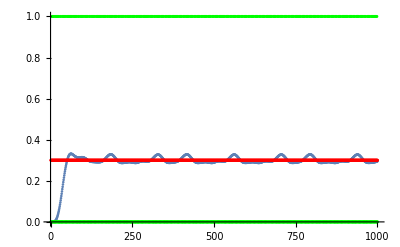

```mathematica
Show[ListPlot[MyFilter[quantizedDitheredSignalGolden],PlotRange->{0,1}],ListPlot[originalConstantSignal,PlotStyle->Red],ListPlot[quantizedDitheredSignalGolden,PlotStyle->Green]]
```

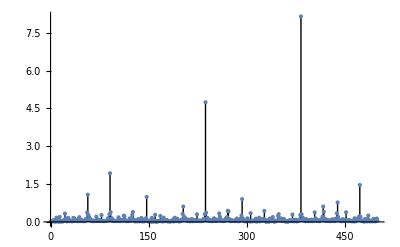

```mathematica
MyPeriodogram[ditheredSignalErrorGolden]
```

```mathematica
Image[Join[{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},{quantizedDitheredSignalGolden},1]]
```

-Graphics-

```mathematica
sineFunction[x_]:= 0.5 + Sin[x/250*2*π]*0.5;

originalSineSignal = sineFunction[#1]&/@Range[sampleCount];
(* 1 bit quantization of sine signal*)
quantizedSineSignal = Round[sineFunction[#1]]&/@Range[sampleCount];
```

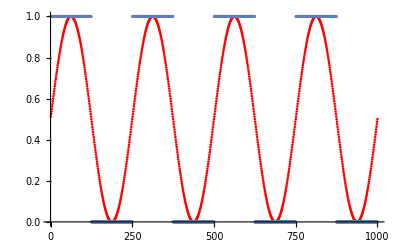

```mathematica
Show[ListPlot[originalSineSignal,PlotStyle->Red],
ListPlot[quantizedSineSignal]]
```

```mathematica
sineSignalError = originalSineSignal-quantizedSineSignal;
```

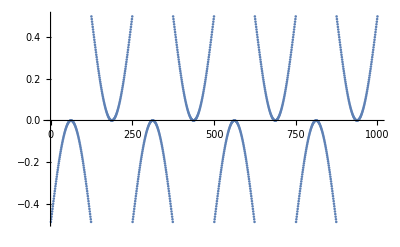

```mathematica
ListPlot[sineSignalError]
```

```mathematica
(*Average error... not bad, huh?*)
```

```mathematica
Mean[sineSignalError]
```

0.004

```mathematica
(*But error has lots of low and high frequencies*)
```

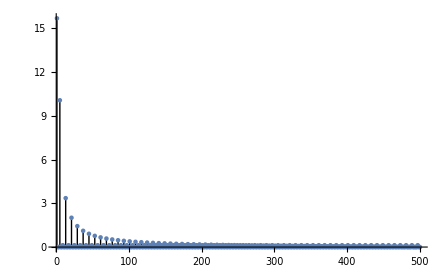

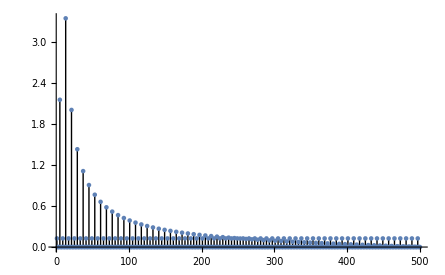

```mathematica
MyPeriodogram[quantizedSineSignal]
MyPeriodogram[sineSignalError]
```

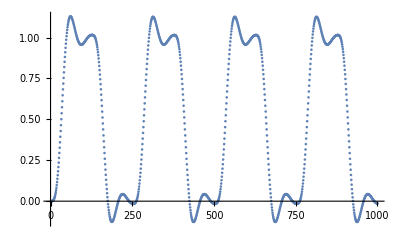

```mathematica
ListPlot[MyFilter[quantizedSineSignal]]
```

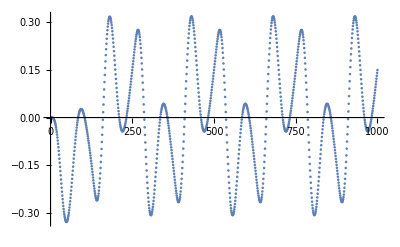

```mathematica
ListPlot[MyFilter[sineSignalError]]
```

```mathematica
(* 1 bit quantization of dithered sine signal*)
quantizedDitheredSineSignal = Round[sineFunction[#1]+RandomReal[]-0.5]&/@Range[sampleCount];
```

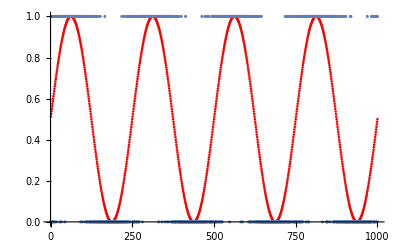

```mathematica
Show[ListPlot[originalSineSignal,PlotStyle->Red],
ListPlot[quantizedDitheredSineSignal]]
```

```mathematica
Image[Join[{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},1]]
ditheredSineSignalError = originalSineSignal-quantizedDitheredSineSignal;
```

-Graphics-

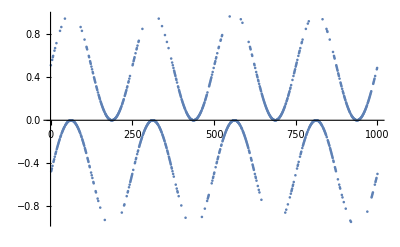

```mathematica
ListPlot[ditheredSineSignalError]
```

```mathematica
ListAnimate[{MyPeriodogram[sineSignalError,Red,{0,4}],MyPeriodogram[ditheredSineSignalError,Black,{0,4}]}]
```

```mathematica
Export["spectrum_quantization_noise_comparison_sine.gif",{MyPeriodogram[sineSignalError,Red,{0,4}],MyPeriodogram[ditheredSineSignalError,Black,{0,4}]},"DisplayDurations"->2];
```

```mathematica
Mean[ditheredSineSignalError]
```

0.006

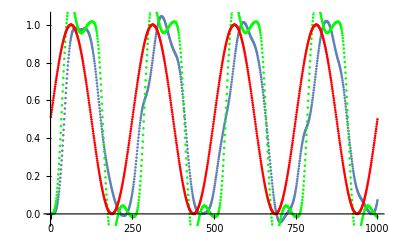

```mathematica
Show[ListPlot[MyFilter[quantizedDitheredSineSignal]],ListPlot[MyFilter[quantizedSineSignal],PlotStyle->Green],ListPlot[originalSineSignal,PlotStyle->Red]]
```

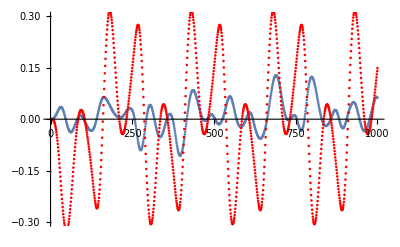

```mathematica
Show[ListPlot[MyFilter[ditheredSineSignalError],PlotRange->{-0.3,0.3}],ListPlot[MyFilter[sineSignalError],PlotStyle->Red]]
```

```mathematica
quantizedDitheredSineSignalGolden = Round[sineFunction[#1]+FractionalPart[GoldenRatio*#1]-0.5]&/@Range[sampleCount];
Image[Join[{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},1]]
```

-Graphics-

```mathematica
ditheredSineSignalGoldenError = originalSineSignal-quantizedDitheredSineSignalGolden;
```

```mathematica
ListAnimate[{MyPeriodogram[sineSignalError,Red,{0,4}],MyPeriodogram[ditheredSineSignalError,Black,{0,4}],MyPeriodogram[ditheredSineSignalGoldenError,Blue,{0,4}]}]
Export["spectrum_quantization_noise_golden__comparison_sine.gif",{MyPeriodogram[sineSignalError,Red,{0,4}],MyPeriodogram[ditheredSineSignalError,Black,{0,4}],MyPeriodogram[ditheredSineSignalGoldenError,Blue,{0,4}]},"DisplayDurations"->2];
```

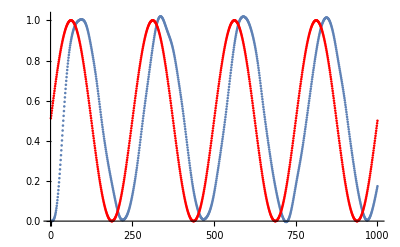

```mathematica
Show[ListPlot[MyFilter[quantizedDitheredSineSignalGolden]],ListPlot[originalSineSignal,PlotStyle->Red]]
```

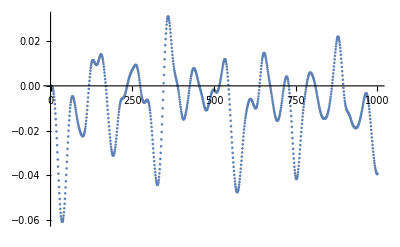

```mathematica
ListPlot[MyFilter[ditheredSineSignalGoldenError]]
```

```mathematica
Image[Join[{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignal},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},{quantizedDitheredSineSignalGolden},1]]
```

-Graphics-